### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Fields mixing at the two-point level

### Keywords

Details

# Fields mixing at the two-point level

In some theories we have two-point functions of different fields, i.e., the two-point matrix is not diagonal in the bosonic part and not off-diagonal for the Grassmann fields.

In this case two additional arguments are required for deriving a DSE or RGE:

The fields have to be define explicitly as commuting or anti-commuting with the option specificFieldDefinitions and the allowed propagators are required as an additional argument to doDSE or doRGE.

doDSE[action, legs, allowedPropagators,specificFieldDefinitions→ fieldDefs] | Derives the DSE specified by legs from action. allowedPropagators tells which propagators are allowed and fieldDefs contains information about the fields being commuting or anti-commuting.
doRG[action, legs, allowedPropagators,specificFieldDefinitions→ fieldDefs] | Derives the RGE specified by legs from action. allowedPropagators tells which propagators are allowed and fieldDefs contains information about the fields being commuting or anti-commuting.

Derive the DSE of an action with three fields which mix at the two-point level. A, φ and φb are bosonic fields, which is indicated by the option specificFieldDefinitions.
In this case also pure φ or pure φb propagators can appear. The possible appearance of such propagators is indicated by giving a third argument to doDSE which contains the additionally possible propagator combinations.

```mathematica
action={{A,A},{φ,φb},{A,φ},{A,φb},{A,φb,φ}};
```

```mathematica
AABosonic=doDSE[action,{A,A},{{φ,φ},{φb,φb}},specificFieldDefinitions->{A,φ,φb}]
```

op[S[{A,i1},{A,i2}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{A,t1},{A,u1}],P[{φb,r1},{A,t1}],P[{φ,s1},{A,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{A,t1},{φ,u1}],P[{φb,r1},{A,t1}],P[{φ,s1},{φ,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{A,t1},{φb,u1}],P[{φb,r1},{A,t1}],P[{φ,s1},{φb,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{A,u1},{φ,t1}],P[{φ,t1},{φb,r1}],P[{φ,s1},{A,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{A,u1},{φb,t1}],P[{φb,r1},{φb,t1}],P[{φ,s1},{A,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{φ,t1},{φ,u1}],P[{φ,t1},{φb,r1}],P[{φ,s1},{φ,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{φ,t1},{φb,u1}],P[{φ,t1},{φb,r1}],P[{φ,s1},{φb,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{φ,u1},{φb,t1}],P[{φb,r1},{φb,t1}],P[{φ,s1},{φ,u1}]]-op[S[{A,i1},{φb,r1},{φ,s1}],V[{A,i2},{φb,t1},{φb,u1}],P[{φb,r1},{φb,t1}],P[{φ,s1},{φb,u1}]]

When plotting the result it is better not to use any specific styles for the fields, because then the fields of the propagators are indicated explicitly.

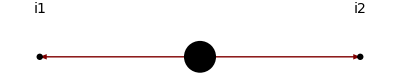
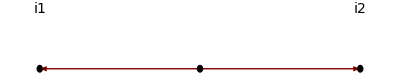
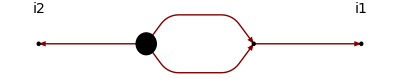
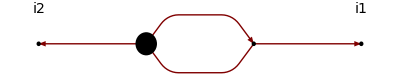
-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  |

```mathematica
DSEPlot[AABosonic]
```

In some cases it is required that the output of doDSE is processed further, since not all graphs have been identified. The reason is that internally doDSE uses the function compareGraphs to identify graphs. Here this function can fail and we have to use compareGraphs2 instead.

In the following example there are three types of graphs which appear twice each. Using identifyGraphs we can add them up.

```mathematica
action={{A,A},{φ,φb},{A,φ},{A,φb},{A,φb,φ},{A,A,A}};
```

```mathematica
AABosonic=doDSE[action,{A,A},{{φ,φ},{φb,φb}},specificFieldDefinitions->{A,φ,φb}];
countTerms@AABosonic
AABosonicId=identifyGraphs[AABosonic,compareFunction->compareGraphs2];
countTerms@AABosonicId
```

19

16

More About

Related Tutorials

Related Wolfram Education Group Courses